# Notebook 08: Tables and Lists

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Lists of Coordinates

### A single position

In two dimensional graphics, the coordinates for a position consist of a list with two elements.

```mathematica
midPoint={5,4};
```

The x coordinate is the First element of the list.

```mathematica
First[midPoint]
```

5

The y coordinate is the Last element of the list.

```mathematica
Last[midPoint]
```

4

You can also use the Part command to extract the first and second parts of the list.

```mathematica
Part[midPoint,1]
```

5

```mathematica
Part[midPoint,2]
```

4

The Part command is usually written using the double-square-bracket shorthand notation.

```mathematica
midPoint⟦1⟧
```

5

```mathematica
midPoint⟦2⟧
```

4

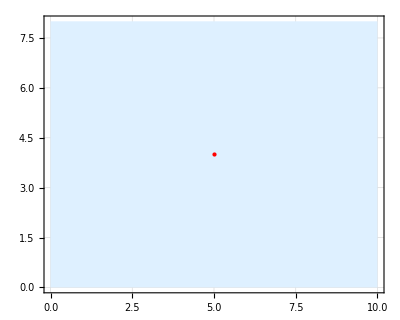

```mathematica
Graphics[{LightBlue,Rectangle[{0,0},{10,8}],Red,PointSize[Large],Point[midPoint]},Frame->True, GridLines->Automatic]
```

### A list of positions

A list of positions corresponds to a list of lists. We can use list commands to generate these lists of positions.

The Range and Reverse commands are described in the textbook

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

The MapThread command can be used to create a list of pairs from a pair of lists

```mathematica
MapThread[List,{Range[10],Range[10]}]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10}}

```mathematica
MapThread[List,{Range[10],Reverse[Range[10]]}]
```

{{1,10},{2,9},{3,8},{4,7},{5,6},{6,5},{7,4},{8,3},{9,2},{10,1}}

These lists of positions correspond to diagonal lines of points

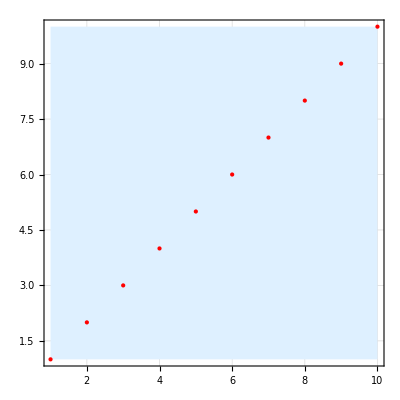

```mathematica
Graphics[{LightBlue,Rectangle[{1,1},{10,10}],Red,PointSize[Large],Point[MapThread[List,{Range[10],Range[10]}]]},Frame->True, GridLines->Automatic]
```

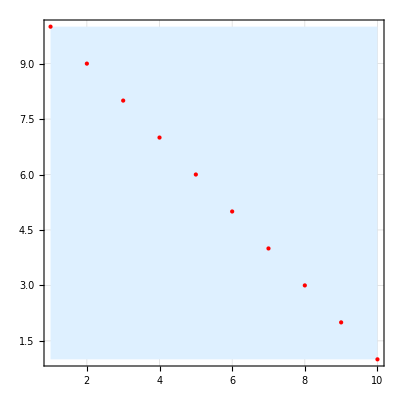

```mathematica
Graphics[{LightBlue,Rectangle[{1,1},{10,10}],Red,PointSize[Large],Point[MapThread[List,{Range[10],Reverse[Range[10]]}]]},Frame->True, GridLines->Automatic]
```

One of the coordinates can change more quickly than the other. You end up with a line with a different slope.

```mathematica
MapThread[List,{Range[3,30,3],Reverse[Range[10]]}]
```

{{3,10},{6,9},{9,8},{12,7},{15,6},{18,5},{21,4},{24,3},{27,2},{30,1}}

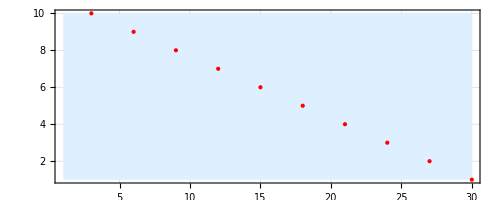

```mathematica
Graphics[{LightBlue,Rectangle[{1,1},{30,10}],Red,PointSize[Large],Point[MapThread[List,{Range[3,30,3],Reverse[Range[10]]}]]},Frame->True, GridLines->Automatic]
```

## Creating lists of coordinates with Table

Often it is easier to use the Table command to generate lists of coordinates. For example, we can replace following list command

```mathematica
MapThread[List,{Range[10],Reverse[Range[10]]}]
```

{{1,10},{2,9},{3,8},{4,7},{5,6},{6,5},{7,4},{8,3},{9,2},{10,1}}

with a simpler Table command

```mathematica
Table[{i,11-i},{i,1,10}]
```

{{1,10},{2,9},{3,8},{4,7},{5,6},{6,5},{7,4},{8,3},{9,2},{10,1}}

We can also use Table to generate lists of lists where one of the elements in each list remains constant. In two dimensional graphics, these coordinate lists correspond to horizontal and vertical lines of positions.

```mathematica
Table[{x,5},{x,1,10}]
```

{{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{9,5},{10,5}}

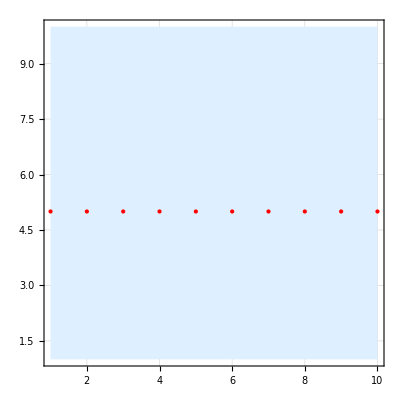

```mathematica
Graphics[{LightBlue,Rectangle[{1,1},{10,10}],Red,PointSize[Large],Point[Table[{x,5},{x,1,10}]]},Frame->True, GridLines->Automatic]
```

```mathematica
Table[{5,y},{y,1,10}]
```

{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10}}

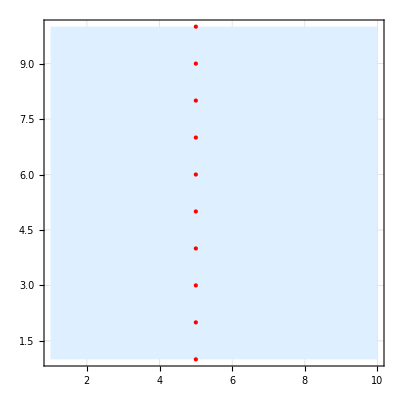

```mathematica
Graphics[{LightBlue,Rectangle[{1,1},{10,10}],Red,PointSize[Large],Point[Table[{5,y},{y,1,10}]]},Frame->True, GridLines->Automatic]
```

We can also make one coordinate random, but not the other. The following example creates 10 coordinate pairs where the y component is always 5, and the x component is randomly chosen to be between 0 and 10. The darker the disk, the more times that particular value for the x coordinate has been chosen.

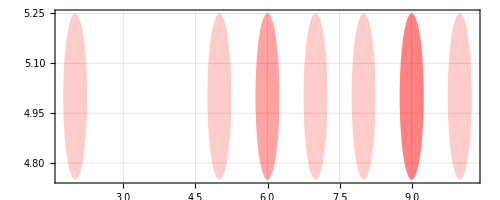

```mathematica
Graphics[{Red,Opacity[.2],Table[Disk[{RandomInteger[10],5},1/4],{10}]},Frame->True, GridLines->Automatic,ImageSize->Full]
```

Here is what the Table command is doing.

```mathematica
Table[Disk[{RandomInteger[10],5},1/4],{10}]
```

{Disk[{7,5},1/4],Disk[{4,5},1/4],Disk[{4,5},1/4],Disk[{0,5},1/4],Disk[{1,5},1/4],Disk[{2,5},1/4],Disk[{0,5},1/4],Disk[{0,5},1/4],Disk[{2,5},1/4],Disk[{7,5},1/4]}

## The order of operations

Sometimes we point the Table command inside a graphics command like Point, and sometimes we put it outside. How do we choose?

The Point command can plot a single point or a list of points.

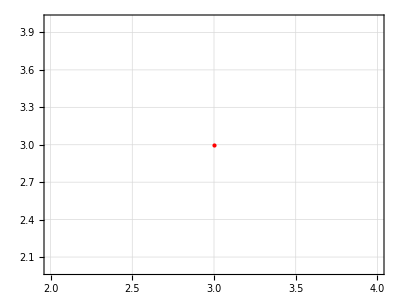

```mathematica
Graphics[{Red,PointSize[Large],Point[{3,3}]},Frame->True, GridLines->Automatic]
```

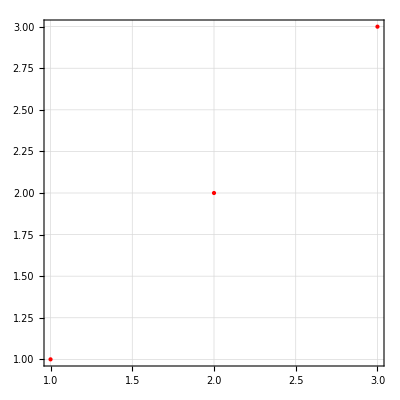

```mathematica
Graphics[{Red,PointSize[Large],Point[{{1,1},{2,2},{3,3}}]},Frame->True, GridLines->Automatic]
```

If we put Table inside of Point, we end up with a more efficient expression.

```mathematica
Point[Table[{i,i},{i,10}]]
```

Point[{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10}}]

```mathematica
Table[Point[{i,i}],{i,10}]
```

{Point[{1,1}],Point[{2,2}],Point[{3,3}],Point[{4,4}],Point[{5,5}],Point[{6,6}],Point[{7,7}],Point[{8,8}],Point[{9,9}],Point[{10,10}]}

Note that both expressions result in the same graphic.

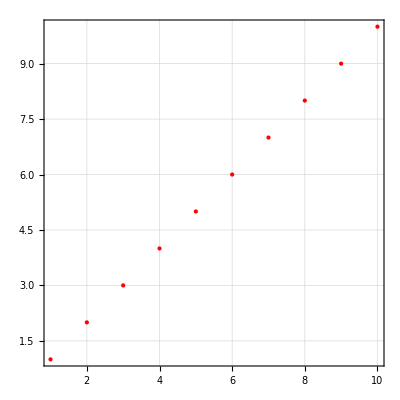

```mathematica
Graphics[{Red,PointSize[Large],Point[Table[{i,i},{i,10}]]},Frame->True, GridLines->Automatic]
```

```mathematica
Graphics[{Red,PointSize[Large],Table[Point[{i,i}],{i,10}]},Frame->True, GridLines->Automatic]
```

-Graphics-

So does this mean we should always put Table inside Point? No. Consider the case where we want to choose a random colour for our points. Each time we evaluate the following expression, all of the points will be plotted in the same random colour.

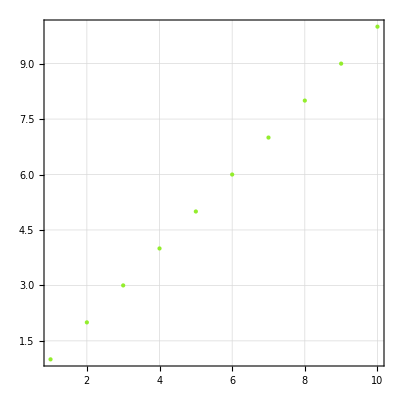

```mathematica
Graphics[{PointSize[Large],RandomColor[],Point[Table[{i,i},{i,10}]]},Frame->True, GridLines->Automatic]
```

But if we want each point to be a different colour, then we have to put Point inside Table.

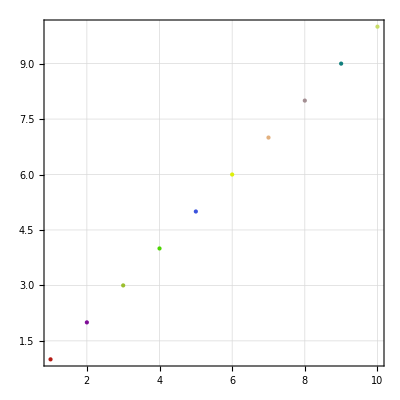

```mathematica
Graphics[{PointSize[Large],Table[{RandomColor[],Point[{i,i}]},{i,10}]},Frame->True, GridLines->Automatic]
```

A command like Disk, which only plots a single element, always has to go inside the Table command.

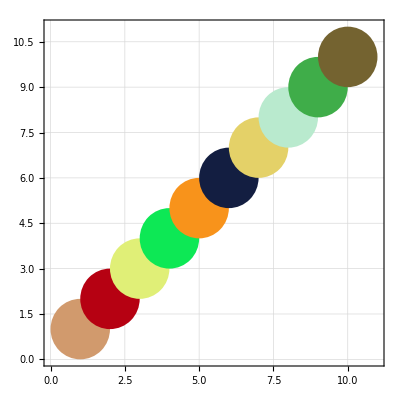

```mathematica
Graphics[{PointSize[Large],Table[{RandomColor[],Disk[{i,i}]},{i,10}]},Frame->True, GridLines->Automatic]
```

## Tables with multiple iterators

### Grids

If you use two iterators, you can generate a grid of coordinates.

```mathematica
Table[{x,y},{x,1,3},{y,4,6}]
```

{{{1,4},{1,5},{1,6}},{{2,4},{2,5},{2,6}},{{3,4},{3,5},{3,6}}}

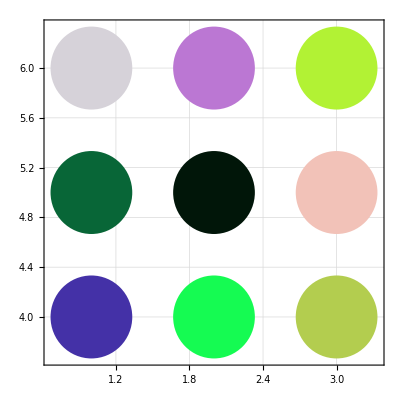

```mathematica
Graphics[{PointSize[Large],Table[{RandomColor[],Disk[{x,y},1/3]},{x,1,3},{y,4,6}]},Frame->True, GridLines->Automatic]
```

### Colour

You can also use multiple iterators to generate colour palettes by adjusting parameter values simultaneously.

```mathematica
rgbExampleList=Table[RGBColor[r,g,b],{r,0,1,.2},{g,.5,1,.1},{b,0,.5,.1}]
```

{{{RGBColor[0., 0.5, 0.],RGBColor[0., 0.5, 0.1],RGBColor[0., 0.5, 0.2],RGBColor[0., 0.5, 0.30000000000000004],RGBColor[0., 0.5, 0.4],RGBColor[0., 0.5, 0.5]},{RGBColor[0., 0.6, 0.],RGBColor[0., 0.6, 0.1],RGBColor[0., 0.6, 0.2],RGBColor[0., 0.6, 0.30000000000000004],RGBColor[0., 0.6, 0.4],RGBColor[0., 0.6, 0.5]},{RGBColor[0., 0.7, 0.],RGBColor[0., 0.7, 0.1],RGBColor[0., 0.7, 0.2],RGBColor[0., 0.7, 0.30000000000000004],RGBColor[0., 0.7, 0.4],RGBColor[0., 0.7, 0.5]},{RGBColor[0., 0.8, 0.],RGBColor[0., 0.8, 0.1],RGBColor[0., 0.8, 0.2],RGBColor[0., 0.8, 0.30000000000000004],RGBColor[0., 0.8, 0.4],RGBColor[0., 0.8, 0.5]},{RGBColor[0., 0.9, 0.],RGBColor[0., 0.9, 0.1],RGBColor[0., 0.9, 0.2],RGBColor[0., 0.9, 0.30000000000000004],RGBColor[0., 0.9, 0.4],RGBColor[0., 0.9, 0.5]},{RGBColor[0., 1., 0.],RGBColor[0., 1., 0.1],RGBColor[0., 1., 0.2],RGBColor[0., 1., 0.30000000000000004],RGBColor[0., 1., 0.4],RGBColor[0., 1., 0.5]}},{{RGBColor[0.2, 0.5, 0.],RGBColor[0.2, 0.5, 0.1],RGBColor[0.2, 0.5, 0.2],RGBColor[0.2, 0.5, 0.30000000000000004],RGBColor[0.2, 0.5, 0.4],RGBColor[0.2, 0.5, 0.5]},{RGBColor[0.2, 0.6, 0.],RGBColor[0.2, 0.6, 0.1],RGBColor[0.2, 0.6, 0.2],RGBColor[0.2, 0.6, 0.30000000000000004],RGBColor[0.2, 0.6, 0.4],RGBColor[0.2, 0.6, 0.5]},{RGBColor[0.2, 0.7, 0.],RGBColor[0.2, 0.7, 0.1],RGBColor[0.2, 0.7, 0.2],RGBColor[0.2, 0.7, 0.30000000000000004],RGBColor[0.2, 0.7, 0.4],RGBColor[0.2, 0.7, 0.5]},{RGBColor[0.2, 0.8, 0.],RGBColor[0.2, 0.8, 0.1],RGBColor[0.2, 0.8, 0.2],RGBColor[0.2, 0.8, 0.30000000000000004],RGBColor[0.2, 0.8, 0.4],RGBColor[0.2, 0.8, 0.5]},{RGBColor[0.2, 0.9, 0.],RGBColor[0.2, 0.9, 0.1],RGBColor[0.2, 0.9, 0.2],RGBColor[0.2, 0.9, 0.30000000000000004],RGBColor[0.2, 0.9, 0.4],RGBColor[0.2, 0.9, 0.5]},{RGBColor[0.2, 1., 0.],RGBColor[0.2, 1., 0.1],RGBColor[0.2, 1., 0.2],RGBColor[0.2, 1., 0.30000000000000004],RGBColor[0.2, 1., 0.4],RGBColor[0.2, 1., 0.5]}},{{RGBColor[0.4, 0.5, 0.],RGBColor[0.4, 0.5, 0.1],RGBColor[0.4, 0.5, 0.2],RGBColor[0.4, 0.5, 0.30000000000000004],RGBColor[0.4, 0.5, 0.4],RGBColor[0.4, 0.5, 0.5]},{RGBColor[0.4, 0.6, 0.],RGBColor[0.4, 0.6, 0.1],RGBColor[0.4, 0.6, 0.2],RGBColor[0.4, 0.6, 0.30000000000000004],RGBColor[0.4, 0.6, 0.4],RGBColor[0.4, 0.6, 0.5]},{RGBColor[0.4, 0.7, 0.],RGBColor[0.4, 0.7, 0.1],RGBColor[0.4, 0.7, 0.2],RGBColor[0.4, 0.7, 0.30000000000000004],RGBColor[0.4, 0.7, 0.4],RGBColor[0.4, 0.7, 0.5]},{RGBColor[0.4, 0.8, 0.],RGBColor[0.4, 0.8, 0.1],RGBColor[0.4, 0.8, 0.2],RGBColor[0.4, 0.8, 0.30000000000000004],RGBColor[0.4, 0.8, 0.4],RGBColor[0.4, 0.8, 0.5]},{RGBColor[0.4, 0.9, 0.],RGBColor[0.4, 0.9, 0.1],RGBColor[0.4, 0.9, 0.2],RGBColor[0.4, 0.9, 0.30000000000000004],RGBColor[0.4, 0.9, 0.4],RGBColor[0.4, 0.9, 0.5]},{RGBColor[0.4, 1., 0.],RGBColor[0.4, 1., 0.1],RGBColor[0.4, 1., 0.2],RGBColor[0.4, 1., 0.30000000000000004],RGBColor[0.4, 1., 0.4],RGBColor[0.4, 1., 0.5]}},{{RGBColor[0.6000000000000001, 0.5, 0.],RGBColor[0.6000000000000001, 0.5, 0.1],RGBColor[0.6000000000000001, 0.5, 0.2],RGBColor[0.6000000000000001, 0.5, 0.30000000000000004],RGBColor[0.6000000000000001, 0.5, 0.4],RGBColor[0.6000000000000001, 0.5, 0.5]},{RGBColor[0.6000000000000001, 0.6, 0.],RGBColor[0.6000000000000001, 0.6, 0.1],RGBColor[0.6000000000000001, 0.6, 0.2],RGBColor[0.6000000000000001, 0.6, 0.30000000000000004],RGBColor[0.6000000000000001, 0.6, 0.4],RGBColor[0.6000000000000001, 0.6, 0.5]},{RGBColor[0.6000000000000001, 0.7, 0.],RGBColor[0.6000000000000001, 0.7, 0.1],RGBColor[0.6000000000000001, 0.7, 0.2],RGBColor[0.6000000000000001, 0.7, 0.30000000000000004],RGBColor[0.6000000000000001, 0.7, 0.4],RGBColor[0.6000000000000001, 0.7, 0.5]},{RGBColor[0.6000000000000001, 0.8, 0.],RGBColor[0.6000000000000001, 0.8, 0.1],RGBColor[0.6000000000000001, 0.8, 0.2],RGBColor[0.6000000000000001, 0.8, 0.30000000000000004],RGBColor[0.6000000000000001, 0.8, 0.4],RGBColor[0.6000000000000001, 0.8, 0.5]},{RGBColor[0.6000000000000001, 0.9, 0.],RGBColor[0.6000000000000001, 0.9, 0.1],RGBColor[0.6000000000000001, 0.9, 0.2],RGBColor[0.6000000000000001, 0.9, 0.30000000000000004],RGBColor[0.6000000000000001, 0.9, 0.4],RGBColor[0.6000000000000001, 0.9, 0.5]},{RGBColor[0.6000000000000001, 1., 0.],RGBColor[0.6000000000000001, 1., 0.1],RGBColor[0.6000000000000001, 1., 0.2],RGBColor[0.6000000000000001, 1., 0.30000000000000004],RGBColor[0.6000000000000001, 1., 0.4],RGBColor[0.6000000000000001, 1., 0.5]}},{{RGBColor[0.8, 0.5, 0.],RGBColor[0.8, 0.5, 0.1],RGBColor[0.8, 0.5, 0.2],RGBColor[0.8, 0.5, 0.30000000000000004],RGBColor[0.8, 0.5, 0.4],RGBColor[0.8, 0.5, 0.5]},{RGBColor[0.8, 0.6, 0.],RGBColor[0.8, 0.6, 0.1],RGBColor[0.8, 0.6, 0.2],RGBColor[0.8, 0.6, 0.30000000000000004],RGBColor[0.8, 0.6, 0.4],RGBColor[0.8, 0.6, 0.5]},{RGBColor[0.8, 0.7, 0.],RGBColor[0.8, 0.7, 0.1],RGBColor[0.8, 0.7, 0.2],RGBColor[0.8, 0.7, 0.30000000000000004],RGBColor[0.8, 0.7, 0.4],RGBColor[0.8, 0.7, 0.5]},{RGBColor[0.8, 0.8, 0.],RGBColor[0.8, 0.8, 0.1],RGBColor[0.8, 0.8, 0.2],RGBColor[0.8, 0.8, 0.30000000000000004],RGBColor[0.8, 0.8, 0.4],RGBColor[0.8, 0.8, 0.5]},{RGBColor[0.8, 0.9, 0.],RGBColor[0.8, 0.9, 0.1],RGBColor[0.8, 0.9, 0.2],RGBColor[0.8, 0.9, 0.30000000000000004],RGBColor[0.8, 0.9, 0.4],RGBColor[0.8, 0.9, 0.5]},{RGBColor[0.8, 1., 0.],RGBColor[0.8, 1., 0.1],RGBColor[0.8, 1., 0.2],RGBColor[0.8, 1., 0.30000000000000004],RGBColor[0.8, 1., 0.4],RGBColor[0.8, 1., 0.5]}},{{RGBColor[1., 0.5, 0.],RGBColor[1., 0.5, 0.1],RGBColor[1., 0.5, 0.2],RGBColor[1., 0.5, 0.30000000000000004],RGBColor[1., 0.5, 0.4],RGBColor[1., 0.5, 0.5]},{RGBColor[1., 0.6, 0.],RGBColor[1., 0.6, 0.1],RGBColor[1., 0.6, 0.2],RGBColor[1., 0.6, 0.30000000000000004],RGBColor[1., 0.6, 0.4],RGBColor[1., 0.6, 0.5]},{RGBColor[1., 0.7, 0.],RGBColor[1., 0.7, 0.1],RGBColor[1., 0.7, 0.2],RGBColor[1., 0.7, 0.30000000000000004],RGBColor[1., 0.7, 0.4],RGBColor[1., 0.7, 0.5]},{RGBColor[1., 0.8, 0.],RGBColor[1., 0.8, 0.1],RGBColor[1., 0.8, 0.2],RGBColor[1., 0.8, 0.30000000000000004],RGBColor[1., 0.8, 0.4],RGBColor[1., 0.8, 0.5]},{RGBColor[1., 0.9, 0.],RGBColor[1., 0.9, 0.1],RGBColor[1., 0.9, 0.2],RGBColor[1., 0.9, 0.30000000000000004],RGBColor[1., 0.9, 0.4],RGBColor[1., 0.9, 0.5]},{RGBColor[1., 1., 0.],RGBColor[1., 1., 0.1],RGBColor[1., 1., 0.2],RGBColor[1., 1., 0.30000000000000004],RGBColor[1., 1., 0.4],RGBColor[1., 1., 0.5]}}}

```mathematica
hueExampleList=Table[Hue[h,s,b],{h,.5,1,.1},{s,0,1,.2},{b,0,1,.2}]
```

{{{Hue[0.5, 0., 0.],Hue[0.5, 0., 0.2],Hue[0.5, 0., 0.4],Hue[0.5, 0., 0.6000000000000001],Hue[0.5, 0., 0.8],Hue[0.5, 0., 1.]},{Hue[0.5, 0.2, 0.],Hue[0.5, 0.2, 0.2],Hue[0.5, 0.2, 0.4],Hue[0.5, 0.2, 0.6000000000000001],Hue[0.5, 0.2, 0.8],Hue[0.5, 0.2, 1.]},{Hue[0.5, 0.4, 0.],Hue[0.5, 0.4, 0.2],Hue[0.5, 0.4, 0.4],Hue[0.5, 0.4, 0.6000000000000001],Hue[0.5, 0.4, 0.8],Hue[0.5, 0.4, 1.]},{Hue[0.5, 0.6000000000000001, 0.],Hue[0.5, 0.6000000000000001, 0.2],Hue[0.5, 0.6000000000000001, 0.4],Hue[0.5, 0.6000000000000001, 0.6000000000000001],Hue[0.5, 0.6000000000000001, 0.8],Hue[0.5, 0.6000000000000001, 1.]},{Hue[0.5, 0.8, 0.],Hue[0.5, 0.8, 0.2],Hue[0.5, 0.8, 0.4],Hue[0.5, 0.8, 0.6000000000000001],Hue[0.5, 0.8, 0.8],Hue[0.5, 0.8, 1.]},{Hue[0.5, 1., 0.],Hue[0.5, 1., 0.2],Hue[0.5, 1., 0.4],Hue[0.5, 1., 0.6000000000000001],Hue[0.5, 1., 0.8],Hue[0.5, 1., 1.]}},{{Hue[0.6, 0., 0.],Hue[0.6, 0., 0.2],Hue[0.6, 0., 0.4],Hue[0.6, 0., 0.6000000000000001],Hue[0.6, 0., 0.8],Hue[0.6, 0., 1.]},{Hue[0.6, 0.2, 0.],Hue[0.6, 0.2, 0.2],Hue[0.6, 0.2, 0.4],Hue[0.6, 0.2, 0.6000000000000001],Hue[0.6, 0.2, 0.8],Hue[0.6, 0.2, 1.]},{Hue[0.6, 0.4, 0.],Hue[0.6, 0.4, 0.2],Hue[0.6, 0.4, 0.4],Hue[0.6, 0.4, 0.6000000000000001],Hue[0.6, 0.4, 0.8],Hue[0.6, 0.4, 1.]},{Hue[0.6, 0.6000000000000001, 0.],Hue[0.6, 0.6000000000000001, 0.2],Hue[0.6, 0.6000000000000001, 0.4],Hue[0.6, 0.6000000000000001, 0.6000000000000001],Hue[0.6, 0.6000000000000001, 0.8],Hue[0.6, 0.6000000000000001, 1.]},{Hue[0.6, 0.8, 0.],Hue[0.6, 0.8, 0.2],Hue[0.6, 0.8, 0.4],Hue[0.6, 0.8, 0.6000000000000001],Hue[0.6, 0.8, 0.8],Hue[0.6, 0.8, 1.]},{Hue[0.6, 1., 0.],Hue[0.6, 1., 0.2],Hue[0.6, 1., 0.4],Hue[0.6, 1., 0.6000000000000001],Hue[0.6, 1., 0.8],Hue[0.6, 1., 1.]}},{{Hue[0.7, 0., 0.],Hue[0.7, 0., 0.2],Hue[0.7, 0., 0.4],Hue[0.7, 0., 0.6000000000000001],Hue[0.7, 0., 0.8],Hue[0.7, 0., 1.]},{Hue[0.7, 0.2, 0.],Hue[0.7, 0.2, 0.2],Hue[0.7, 0.2, 0.4],Hue[0.7, 0.2, 0.6000000000000001],Hue[0.7, 0.2, 0.8],Hue[0.7, 0.2, 1.]},{Hue[0.7, 0.4, 0.],Hue[0.7, 0.4, 0.2],Hue[0.7, 0.4, 0.4],Hue[0.7, 0.4, 0.6000000000000001],Hue[0.7, 0.4, 0.8],Hue[0.7, 0.4, 1.]},{Hue[0.7, 0.6000000000000001, 0.],Hue[0.7, 0.6000000000000001, 0.2],Hue[0.7, 0.6000000000000001, 0.4],Hue[0.7, 0.6000000000000001, 0.6000000000000001],Hue[0.7, 0.6000000000000001, 0.8],Hue[0.7, 0.6000000000000001, 1.]},{Hue[0.7, 0.8, 0.],Hue[0.7, 0.8, 0.2],Hue[0.7, 0.8, 0.4],Hue[0.7, 0.8, 0.6000000000000001],Hue[0.7, 0.8, 0.8],Hue[0.7, 0.8, 1.]},{Hue[0.7, 1., 0.],Hue[0.7, 1., 0.2],Hue[0.7, 1., 0.4],Hue[0.7, 1., 0.6000000000000001],Hue[0.7, 1., 0.8],Hue[0.7, 1., 1.]}},{{Hue[0.8, 0., 0.],Hue[0.8, 0., 0.2],Hue[0.8, 0., 0.4],Hue[0.8, 0., 0.6000000000000001],Hue[0.8, 0., 0.8],Hue[0.8, 0., 1.]},{Hue[0.8, 0.2, 0.],Hue[0.8, 0.2, 0.2],Hue[0.8, 0.2, 0.4],Hue[0.8, 0.2, 0.6000000000000001],Hue[0.8, 0.2, 0.8],Hue[0.8, 0.2, 1.]},{Hue[0.8, 0.4, 0.],Hue[0.8, 0.4, 0.2],Hue[0.8, 0.4, 0.4],Hue[0.8, 0.4, 0.6000000000000001],Hue[0.8, 0.4, 0.8],Hue[0.8, 0.4, 1.]},{Hue[0.8, 0.6000000000000001, 0.],Hue[0.8, 0.6000000000000001, 0.2],Hue[0.8, 0.6000000000000001, 0.4],Hue[0.8, 0.6000000000000001, 0.6000000000000001],Hue[0.8, 0.6000000000000001, 0.8],Hue[0.8, 0.6000000000000001, 1.]},{Hue[0.8, 0.8, 0.],Hue[0.8, 0.8, 0.2],Hue[0.8, 0.8, 0.4],Hue[0.8, 0.8, 0.6000000000000001],Hue[0.8, 0.8, 0.8],Hue[0.8, 0.8, 1.]},{Hue[0.8, 1., 0.],Hue[0.8, 1., 0.2],Hue[0.8, 1., 0.4],Hue[0.8, 1., 0.6000000000000001],Hue[0.8, 1., 0.8],Hue[0.8, 1., 1.]}},{{Hue[0.9, 0., 0.],Hue[0.9, 0., 0.2],Hue[0.9, 0., 0.4],Hue[0.9, 0., 0.6000000000000001],Hue[0.9, 0., 0.8],Hue[0.9, 0., 1.]},{Hue[0.9, 0.2, 0.],Hue[0.9, 0.2, 0.2],Hue[0.9, 0.2, 0.4],Hue[0.9, 0.2, 0.6000000000000001],Hue[0.9, 0.2, 0.8],Hue[0.9, 0.2, 1.]},{Hue[0.9, 0.4, 0.],Hue[0.9, 0.4, 0.2],Hue[0.9, 0.4, 0.4],Hue[0.9, 0.4, 0.6000000000000001],Hue[0.9, 0.4, 0.8],Hue[0.9, 0.4, 1.]},{Hue[0.9, 0.6000000000000001, 0.],Hue[0.9, 0.6000000000000001, 0.2],Hue[0.9, 0.6000000000000001, 0.4],Hue[0.9, 0.6000000000000001, 0.6000000000000001],Hue[0.9, 0.6000000000000001, 0.8],Hue[0.9, 0.6000000000000001, 1.]},{Hue[0.9, 0.8, 0.],Hue[0.9, 0.8, 0.2],Hue[0.9, 0.8, 0.4],Hue[0.9, 0.8, 0.6000000000000001],Hue[0.9, 0.8, 0.8],Hue[0.9, 0.8, 1.]},{Hue[0.9, 1., 0.],Hue[0.9, 1., 0.2],Hue[0.9, 1., 0.4],Hue[0.9, 1., 0.6000000000000001],Hue[0.9, 1., 0.8],Hue[0.9, 1., 1.]}},{{Hue[1., 0., 0.],Hue[1., 0., 0.2],Hue[1., 0., 0.4],Hue[1., 0., 0.6000000000000001],Hue[1., 0., 0.8],Hue[1., 0., 1.]},{Hue[1., 0.2, 0.],Hue[1., 0.2, 0.2],Hue[1., 0.2, 0.4],Hue[1., 0.2, 0.6000000000000001],Hue[1., 0.2, 0.8],Hue[1., 0.2, 1.]},{Hue[1., 0.4, 0.],Hue[1., 0.4, 0.2],Hue[1., 0.4, 0.4],Hue[1., 0.4, 0.6000000000000001],Hue[1., 0.4, 0.8],Hue[1., 0.4, 1.]},{Hue[1., 0.6000000000000001, 0.],Hue[1., 0.6000000000000001, 0.2],Hue[1., 0.6000000000000001, 0.4],Hue[1., 0.6000000000000001, 0.6000000000000001],Hue[1., 0.6000000000000001, 0.8],Hue[1., 0.6000000000000001, 1.]},{Hue[1., 0.8, 0.],Hue[1., 0.8, 0.2],Hue[1., 0.8, 0.4],Hue[1., 0.8, 0.6000000000000001],Hue[1., 0.8, 0.8],Hue[1., 0.8, 1.]},{Hue[1., 1., 0.],Hue[1., 1., 0.2],Hue[1., 1., 0.4],Hue[1., 1., 0.6000000000000001],Hue[1., 1., 0.8],Hue[1., 1., 1.]}}}

Note that the output of these Table commands are lists of lists of lists. That is to say that they have three levels of nesting. We can use the Part command to pull out sublists.

### Parts of lists

This is the first sublist.

```mathematica
Part[hueExampleList,1]
```

{{Hue[0.5, 0., 0.],Hue[0.5, 0., 0.2],Hue[0.5, 0., 0.4],Hue[0.5, 0., 0.6000000000000001],Hue[0.5, 0., 0.8],Hue[0.5, 0., 1.]},{Hue[0.5, 0.2, 0.],Hue[0.5, 0.2, 0.2],Hue[0.5, 0.2, 0.4],Hue[0.5, 0.2, 0.6000000000000001],Hue[0.5, 0.2, 0.8],Hue[0.5, 0.2, 1.]},{Hue[0.5, 0.4, 0.],Hue[0.5, 0.4, 0.2],Hue[0.5, 0.4, 0.4],Hue[0.5, 0.4, 0.6000000000000001],Hue[0.5, 0.4, 0.8],Hue[0.5, 0.4, 1.]},{Hue[0.5, 0.6000000000000001, 0.],Hue[0.5, 0.6000000000000001, 0.2],Hue[0.5, 0.6000000000000001, 0.4],Hue[0.5, 0.6000000000000001, 0.6000000000000001],Hue[0.5, 0.6000000000000001, 0.8],Hue[0.5, 0.6000000000000001, 1.]},{Hue[0.5, 0.8, 0.],Hue[0.5, 0.8, 0.2],Hue[0.5, 0.8, 0.4],Hue[0.5, 0.8, 0.6000000000000001],Hue[0.5, 0.8, 0.8],Hue[0.5, 0.8, 1.]},{Hue[0.5, 1., 0.],Hue[0.5, 1., 0.2],Hue[0.5, 1., 0.4],Hue[0.5, 1., 0.6000000000000001],Hue[0.5, 1., 0.8],Hue[0.5, 1., 1.]}}

This is the second part of the first sublist.

```mathematica
Part[Part[hueExampleList,1],2]
```

{Hue[0.5, 0.2, 0.],Hue[0.5, 0.2, 0.2],Hue[0.5, 0.2, 0.4],Hue[0.5, 0.2, 0.6000000000000001],Hue[0.5, 0.2, 0.8],Hue[0.5, 0.2, 1.]}

We can also write this using shorthand notation.

```mathematica
hueExampleList⟦1,2⟧
```

{Hue[0.5, 0.2, 0.],Hue[0.5, 0.2, 0.2],Hue[0.5, 0.2, 0.4],Hue[0.5, 0.2, 0.6000000000000001],Hue[0.5, 0.2, 0.8],Hue[0.5, 0.2, 1.]}

Here is the third part of the sixth sublist of the RGB example.

```mathematica
rgbExampleList⟦6,3⟧
```

{RGBColor[1., 0.7, 0.],RGBColor[1., 0.7, 0.1],RGBColor[1., 0.7, 0.2],RGBColor[1., 0.7, 0.30000000000000004],RGBColor[1., 0.7, 0.4],RGBColor[1., 0.7, 0.5]}

## Iterating by choosing elements from a list

Suppose you want to put copies of a graphic element evenly distributed at points around a circle. Let’s try to draw a flower as an example. As we have seen, you can use the CirclePoints command to find the coordinates of centre points for the petals.

```mathematica
CirclePoints[6]
```

{{1/2,-(√3)/2},{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2}}

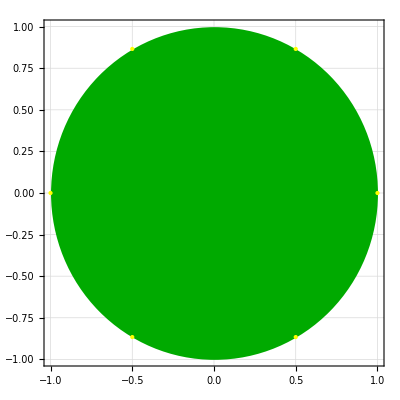

```mathematica
Graphics[{Darker[Green],Disk[],PointSize[Large],Yellow,Point[CirclePoints[6]]},Frame->True,GridLines->Automatic]
```

Now we can place each of the petals. First we need a version of the Table command that uses a list of elements as the iterator. In the following command, p takes on the values 2, 3 and 5.

```mathematica
Table[p,{p,{2,3,5}}]
```

{2,3,5}

If we sample the CirclePoints list with our iterator we can place each petal as follows.

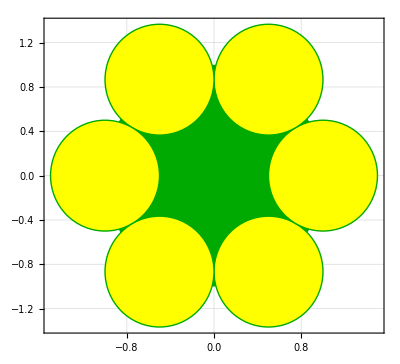

```mathematica
Graphics[{Darker[Green],Disk[],Thick,Table[{Yellow,Disk[p,1/2],Darker[Green],Circle[p,1/2]},{p,CirclePoints[6]}]},Frame->True,GridLines->Automatic]
```

We can change the opacity and size of different elements to get interesting variations

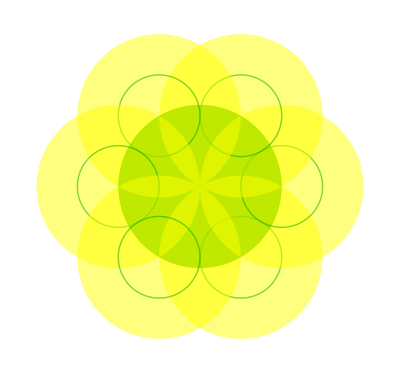

```mathematica
Graphics[{Darker[Green],Disk[],Thick,Opacity[1/2],Table[{Yellow,Disk[p,1],Darker[Green],Circle[p,1/2]},{p,CirclePoints[6]}]}]
```

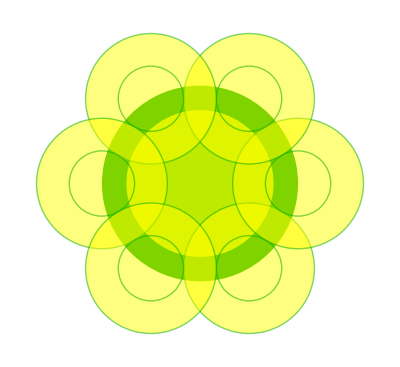

```mathematica
Graphics[{Darker[Green],Disk[],Yellow,Opacity[3/4],Disk[{0,0},3/4],Thick,Table[{Opacity[1/2],Yellow,Disk[p,2/3],Darker[Green],Circle[p,1/3],Circle[p,2/3]},{p,CirclePoints[6]}]}]
```

We change the number of petals simply by changing the number of circle points we generate.

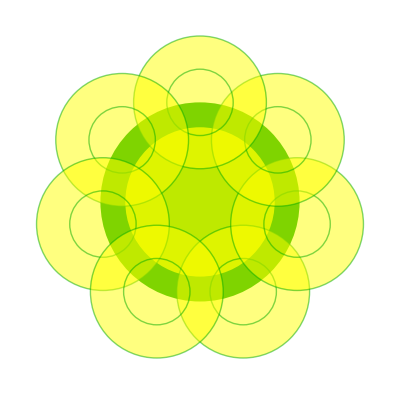

```mathematica
Graphics[{Darker[Green],Disk[],Yellow,Opacity[3/4],Disk[{0,0},3/4],Thick,Table[{Opacity[1/2],Yellow,Disk[p,2/3],Darker[Green],Circle[p,1/3],Circle[p,2/3]},{p,CirclePoints[7]}]}]
```

N.B. Things get tricky if we try to use ellipses for our petals instead of disks or circles. Why?

## In-Class Activity

### Draw a picture using the Graphics and Table commands.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course